# Unitarity Bound Plots.

## NOTE |Re[a_0]|<0.5 in the kinematically allowed region for unitarity to be respected.

## Formulae from 1805.07306.

```mathematica
(*Definitions from 1805.07306*)
λ[s_,mi2_, mj2_]:=1/s^2(s^2+mi2^2+mj2^2-2mi2 mj2 -2 s mi2 -2s mj2)(*eq.7*)
modp[s_,mi2_,mj2_]:=1/2 √(s*λ[s,mi2,mj2]) (*eq.8*)
Ei[s_,mi2_,mj2_]:=(s+mi2-mj2)/(2 √s) (*eq.8*)
E1[s_]:=(s+m12-m22)/(2 √s)
E3[s_]:=(s+m32-m42)/(2 √s)

ft[s_,m12_,m22_,m32_,m42_,m52_]:=1/s 1/(λ[s,m12,m22]*λ[s,m32,m42])^(1/4)Log[(m12+m32-m52-2E1[s]*Ei[s,m32,m42]+2modp[s,m12,m22]*modp[s,m32,m42])/(m12+m32-m52-2E1[s]*Ei[s,m32,m42]-2modp[s,m12,m22]*modp[s,m32,m42])](*eq. 9*)
fu[s_,m12_,m22_,m32_,m42_,m52_]:=ft[s,m12,m22,m42,m32,m52](*eq. 9*)

a0[s_]:=-2^(-1/2(delta12+delta34))/(16 π)((λ[s,m12,m22]*λ[s,m32,m42])^(1/4)(λ1234+(κ125*κ345)/(s-m52s))-κ135*κ245 *ft[s,m12,m22,m32,m42,m52t]-κ145*κ235*fu[s,m12,m22,m32,m42,m52u])(*eq. 10*)
```

## Kinematic Poles (Still not quite correct)

```mathematica
(*Kinematically Accessible Final State*)
minrootS = √(m12+2 √(m12*m22)+m22);

(*WHEN THERE IS ONLY ONE s, t & u DIAGRAM*)
sPole = √m52s; (*s pole is very straightforward*)

(*IF m1 > m2 + m5 OR m2 > m1 + m5:*)
tPole = If[√m12>√m22+√m52t ||√m22>√m12+√m52t ,√m12+√m22+1/2(-√m52t+√((-4 √m12+√m52t)(-4 √m22+√m52t))),0];(*eq. 15*)
uPole = If[m52u==0,If[m22>m12, √(√(3m12*m22)+m22+m12),√(√(3m12*m22)+m22+m12)],
         If[m52u>0&&(√m12>√m22+√m52u ||√m22>√m12+√m52u),(m12+m22-2 √(m12*m22))/(√m52u),0]];
```

## Unitarity Bound Plots in Symmetric Phase.

### Test Points (PUT THE ONE YOU WANT TO SEE LAST!):

```mathematica
(*Van der Woude*)
(*Point B*)tVdW ={mσ2->400^2,mη2->672^2,m2->4848,λσ->25.5,λa->15.2,c->4091, F->3,p->1,fpi->90*√(3/2),Tn->145.3,Tc->145.8};
(*Point C*)tVdW={mσ2->291^2,mη2->328^2,m2->24371,λσ->14.8,λa->14.0,c->1196.,F->3,p->1,fpi->74*√(3/2),Tn->99.9,Tc->100.5};
```

```mathematica
(*Ours*)
tO= {mσ2->170000.,mη2->100.,m2->85016.66666666670,λσ->0.17,λa->3.24,c->10^-10, F->6,p->1,fpi->1000.,Tn->250,Tc->288};
tO={mσ2->90000.,mη2->100.,m2->45016.66666666700,λσ->0.09,λa->1.75,c->10^-10,F->6,p->1,fpi->1000.,Tn->195.,Tc->240.}; (*THIS POINT HAS BEST UNITARY BEHAVIOUR*)
tO={mσ2->210000.,mη2->2950.,m2->105491.66666666700,λσ->0.212,λa->3.24,c->2.95*10^-9,F->6,p->1,fpi->1000.,Tn->271.,Tc->303.};
```

### Couplings:

```mathematica
SymPhase={
λσσσσ->3λσ-KroneckerDelta[F p,4]*c*((p F)(p F-1)(p F-2)(p F-3))/F^2, (*CHECK SIGNS!*)
λσσηη->λσ+KroneckerDelta[F p,4]*c*((p F)(p F-1)(p F-2)(p F-3))/F^2,
κσσσ->KroneckerDelta[F p,3]*(-c/F^2*(p F)(p F-1)(p F-2)),
κσηη->KroneckerDelta[F p,3]*(c/F^2*(p F)(p F-1)(p F-2))};
```

### Scattering σ σ -> σ σ :

```mathematica
(*Data from the scattering process. See 'The Question of Unitarity' on DropBox*)
(*This is σ σ->σ σ scattering.*)
ME={λ1234 -> λσσσσ,
κ125 -> κσσσ,
κ345 -> κσσσ,
κ135 -> κσσσ,
κ245 -> κσσσ,
κ145 -> κσσσ,
κ235 -> κσσσ,
delta12 -> 1,
delta34 -> 1,
m12 -> m2,(*The mass of the scattering particle I believe is m^2 in restored phase*)
m22 ->m2,
m32 -> m2,
m42 ->m2,
m52u->m2,
m52t->m2,
m52s->m2};
```

#### Van der Woude

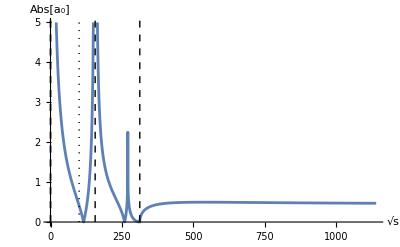

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.tVdW]],
		{rootS,0,4*π*fpi/.tVdW},
		AxesLabel->{√s,Abs[Subscript[a, 0]]},
		PlotRange->{0,5},
		Epilog->{Dashed,Line[{{minrootS/.ME/.tVdW,0},{minrootS/.ME/.tVdW,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
Dashed,Line[{{uPole/.ME/.tVdW,0},{uPole/.ME/.tVdW,10}}],
Dashed,Line[{{tPole/.ME/.tVdW,0},{tPole/.ME/.tVdW,10}}],
Dashed,Line[{{sPole/.ME/.tVdW,0},{sPole/.ME/.tVdW,10}}],
	Dotted,Line[{{Tn/.tVdW,0},{Tn/.tVdW,5}}],(*Vertical line indicating nucleation temperature*)
	Dotted, Line[{{Tc/.tVdW,0},{Tc/.tVdW,5}}] (*DotDashed Vertical line indicating critical temperature*)
 }]
```

```mathematica
(*No t-pole so Technical Minimum kinematically accessible s:*)
minrs=2 √m2/.ME/.tVdW//N
```

312.224

#### Ours

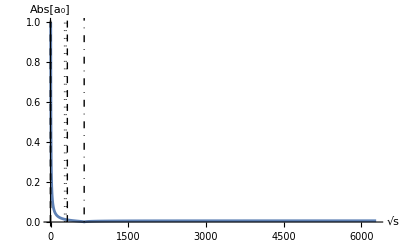

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.tO]],{rootS,0,2π*fpi/.tO},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,1},
Epilog->{DotDashed,Line[{{minrootS/.ME/.tO,0},{minrootS/.ME/.tO,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
Dashed,Line[{{uPole/.ME/.tO,0},{uPole/.ME/.tO,10}}],
Dashed,Line[{{tPole/.ME/.tO,0},{tPole/.ME/.tO,10}}],
Dashed,Line[{{sPole/.ME/.tO,0},{sPole/.ME/.tO,10}}],
	Dotted,Line[{{Tn/.tO,0},{Tn/.tO,10}}],(*Vertical line indicating nucleation temperature*)
	Dotted, Line[{{Tc/.tO,0},{Tc/.tO,10}}] (*DotDashed Vertical line indicating critical temperature*)}]
```

```mathematica
(*No t-pole so Technical Minimum kinematically accessible s:*)
minrs=2 √m2/.ME/.tO
```

649.59

### Scattering σ η -> σ η :

```mathematica
(*Data from the scattering process. See 'The Question of Unitarity' on DropBox*)
ME={λ1234 -> λσσηη,
κ125 -> κσηη,
κ345 -> κσηη,
κ135 -> κσσσ,
κ245 -> κσηη,
κ145 -> κσηη,
κ235 -> κσηη,
delta12 -> 0,
delta34 -> 0,
m12 -> m2,(*The mass of the scattering particle I believe is m^2 in restored phase*)
m22 ->m2,
m32 ->m2,
m42 ->m2,
m52u->m2,
m52t->m2,
m52s->m2};
```

#### Van der Woude

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.tVdW]],
		{rootS,0,4*π*fpi/.tVdW},
		AxesLabel->{√s,Abs[Subscript[a, 0]]},
		PlotRange->{0,5},
		Epilog->{DotDashed,Line[{{minrootS/.ME/.tVdW,0},{minrootS/.ME/.tVdW,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
Dashed,Line[{{uPole/.ME/.tVdW,0},{uPole/.ME/.tVdW,10}}],
Dashed,Line[{{tPole/.ME/.tVdW,0},{tPole/.ME/.tVdW,10}}],
Dashed,Line[{{sPole/.ME/.tVdW,0},{sPole/.ME/.tVdW,10}}],
	Dotted,Line[{{Tn/.tVdW,0},{Tn/.tVdW,5}}],(*Vertical line indicating nucleation temperature*)
	Dotted, Line[{{Tc/.tVdW,0},{Tc/.tVdW,5}}] (*DotDashed Vertical line indicating critical temperature*)
 }]
```

## Unitarity Bound Plots in Broken Phase.

### Couplings:

```mathematica
(*Calculated expressions for the vertices*)
BrokenPhase={λσσηη->λσ+c fpi^(p F-4)((p F)(p F-1)(p F -2)(p F-3))/F^2,(*Numerical factor.?*)
			λσσσσ->3λσ-c fpi^(p F-4)((p F)(p F-1)(p F -2)(p F-3))/F^2,
			ληηηη->3 λσ-c fpi^(p F-4)((p F)(p F-1)(p F -2)(p F-3))/F^2,
			κσηη->λσ*fpi+c fpi^(p F-3)((p F)(p F-1)(p F -2))/F^2,
			κσσσ->3*λσ*fpi-c/F^2 fpi^(p F-3)(p F)(p F-1)(p F-2)};
```

### Scattering σ σ -> σ σ:

```mathematica
(*Data from the scattering process. See 'The Question of Unitarity' on DropBox*)
(*This is σ σ->σ σ scattering.*)
ME={λ1234 -> λσσσσ,
κ125 -> κσσσ,
κ345 -> κσσσ,
κ135 -> κσσσ,
κ245 -> κσσσ,
κ145 -> κσσσ,
κ235 -> κσσσ,
delta12 -> 1,
delta34 -> 1,
m12 -> mσ2,
m22 ->mσ2,
m32 -> mσ2,
m42 ->mσ2,
m52u->mσ2,
m52t->mσ2,
m52s->mσ2};
```

#### Van der Woude

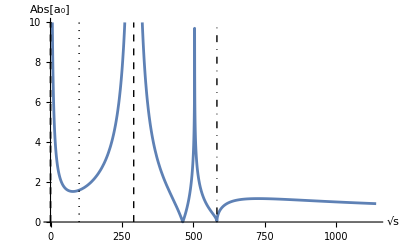

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.BrokenPhase/.tVdW]],{rootS,0,4*π*fpi/.tVdW},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,10},
Epilog->{DotDashed,Line[{{minrootS/.ME/.tVdW,0},{minrootS/.ME/.tVdW,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
Dashed,Line[{{uPole/.ME/.tVdW,0},{uPole/.ME/.tVdW,10}}],
Dashed,Line[{{tPole/.ME/.tVdW,0},{tPole/.ME/.tVdW,10}}],
Dashed,Line[{{sPole/.ME/.tVdW,0},{sPole/.ME/.tVdW,10}}],
	Dotted,Line[{{Tn/.tVdW,0},{Tn/.tVdW,10}}],(*Vertical line indicating nucleation temperature*)
	Dotted, Line[{{Tc/.tVdW,0},{Tc/.tVdW,10}}] (*DotDashed Vertical line indicating critical temperature*)}]
```

```mathematica
(*Technical Minimum s kinematically available*)
2 √m52s/.ME/.tVdW
```

582

```mathematica
(*Weird? minimum s to avoid poles (eq. 15)*)
rootsMin/.ME/.tVdW//N
```

rootsMin

```mathematica
(*Comparison to MM's calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.tVdW
(*Comparison to Symmetric Phase in s->∞ limit:*)
(3*λσ)/(32 π)/.tVdW
```

0.441655

0.441655

#### Ours:

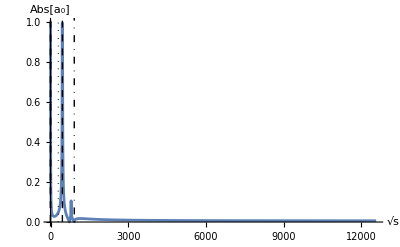

```mathematica
Plot[Abs[Re[a0[rootS^2]/.ME/.BrokenPhase/.{tO}]],{rootS,0,4π*fpi/.tO},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,1},
Epilog->{DotDashed,Line[{{minrootS/.ME/.tO,0},{minrootS/.ME/.tO,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
Dashed,Line[{{uPole/.ME/.tO,0},{uPole/.ME/.tO,10}}],
Dashed,Line[{{tPole/.ME/.tO,0},{tPole/.ME/.tO,10}}],
Dashed,Line[{{sPole/.ME/.tO,0},{sPole/.ME/.tO,10}}],
	Dotted, Line[{{Tc/.tO,0},{Tc/.tO,1}}] (*DotDashed Vertical line indicating critical temperature*)}]
(*Tc=288 and Tn=250*)
```

```mathematica
(*(too?) Conservative minimum s to avoid poles (eq. 15)*)
rootsMin/.ME/.tO//N
```

rootsMin

```mathematica
(*Comparison to MM's Broken Phase Calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.tO
(*Comparison to Symmetric Phase in s->∞ limit:*)
(3*λσ)/(32 π)/.tO
```

0.00661985

0.00632641

### Mixed Scattering σ η’->σ η’:

```mathematica
(*Data from the scattering process. See 'The Question of Unitarity' on DropBox*)
(*This is σ η'->σ η' scattering.*)
ME={λ1234 -> λσσηη,
κ125 -> κσηη,
κ345 -> κσηη,
κ135 -> κσσσ,
κ245 -> κσηη,
κ145 -> κσηη,
κ235 -> κσηη,
delta12 -> 0,
delta34 -> 0,
m12 -> mσ2,
m22 ->mη2,
m32 -> mσ2,
m42 -> mη2,
m52u->mη2,
m52t->mσ2,
m52s->mη2};
```

#### Van der Woude:

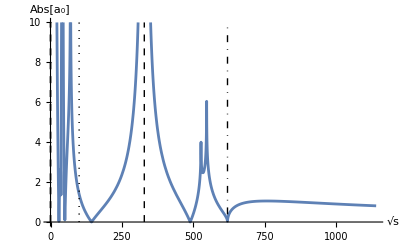

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.BrokenPhase/.tVdW]],{rootS,0,4*π*fpi/.tVdW},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,10},
Epilog->{DotDashed,Line[{{minrootS/.ME/.tVdW,0},{minrootS/.ME/.tVdW,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dashed,Line[{{uPole/.ME/.tVdW,0},{uPole/.ME/.tVdW,10}}],
	Dashed,Line[{{tPole/.ME/.tVdW,0},{tPole/.ME/.tVdW,10}}],
	Dashed,Line[{{sPole/.ME/.tVdW,0},{sPole/.ME/.tVdW,10}}],
	Dotted,Line[{{Tn/.tVdW,0},{Tn/.tVdW,10}}],(*Vertical line indicating nucleation temperature*)
	Dotted, Line[{{Tc/.tVdW,0},{Tc/.tVdW,10}}] (*DotDashed Vertical line indicating critical temperature*)}]
```

```mathematica
(*Comparison to MM's calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.tVdW
(*Comparison to Symmetric Phase in s->∞ limit:*)
(3*λσ)/(32 π)/.tVdW
```

0.441655

0.441655

#### Ours:

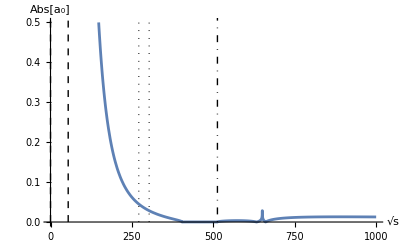

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.BrokenPhase/.{tO}]],{rootS,0,fpi/.tO},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,0.5},
Epilog->{DotDashed,Line[{{minrootS/.ME/.tO,0},{minrootS/.ME/.tO,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dashed,Line[{{uPole/.ME/.tO,0},{uPole/.ME/.tO,10}}],
	Dashed,Line[{{tPole/.ME/.tO,0},{tPole/.ME/.tO,10}}],
	Dashed,Line[{{sPole/.ME/.tO,0},{sPole/.ME/.tO,10}}],
	Dotted,Line[{{Tn/.tO,0},{Tn/.tO,1}}],(*Vertical line indicating nucleation temperature*)
	Dotted, Line[{{Tc/.tO,0},{Tc/.tO,1}}] (*Dotted Vertical line indicating critical temperature*)}]
```

```mathematica
(*Comparison to MM's Calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.tO
(*Comparison to Symmetric Phase in s->∞ limit:*)
(3*λσ)/(32 π)/.tO
```

0.00661985

0.00632641

### Scattering η’η’ -> η’η’:

```mathematica
ME={λ1234 -> ληηηη,
κ125 -> κσηη,
κ345 -> κσηη,
κ135 -> κσηη,
κ245 -> κσηη,
κ145 -> κσηη,
κ235 -> κσηη,
delta12 -> 1,
delta34 -> 1,
m12 -> mη2,
m22 ->mη2,
m32 -> mη2,
m42 ->mη2,
m52u->mσ2,
m52t->mσ2,
m52s->mσ2};
```

#### Van der Woude

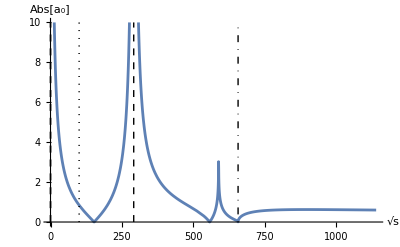

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.BrokenPhase/.tVdW]],{rootS,0,4*π*fpi/.tVdW},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,10},
Epilog->{
	DotDashed,Line[{{minrootS/.ME/.tVdW,0},{minrootS/.ME/.tVdW,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dashed,Line[{{uPole/.ME/.tVdW,0},{uPole/.ME/.tVdW,10}}],
	Dashed,Line[{{tPole/.ME/.tVdW,0},{tPole/.ME/.tVdW,10}}],
	Dashed,Line[{{sPole/.ME/.tVdW,0},{sPole/.ME/.tVdW,10}}],

	Dotted,Line[{{Tn/.tVdW,0},{Tn/.tVdW,10}}],(*Vertical line indicating nucleation temperature*)
	Dotted, Line[{{Tc/.tVdW,0},{Tc/.tVdW,10}}] (*DotDashed Vertical line indicating critical temperature*)}]
```

```mathematica
(*Weird? minimum s to avoid poles (eq. 15)*)
rootsMin/.ME/.tVdW//N
```

rootsMin

```mathematica
(*Comparison to MM's calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.tVdW
(*Comparison to Symmetric Phase in s->∞ limit:*)
(3*λσ)/(32 π)/.tVdW
```

0.441655

0.441655

#### Ours:

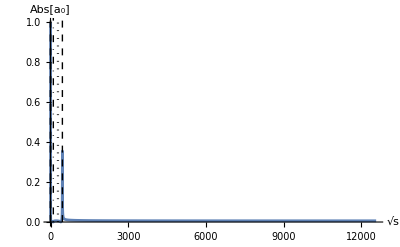

```mathematica
Plot[Abs[Re[a0[rootS^2]/.ME/.BrokenPhase/.{tO}]],{rootS,0,4π*fpi/.tO},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,1},
Epilog->{DotDashed,Line[{{minrootS/.ME/.tO,0},{minrootS/.ME/.tO,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dashed,Line[{{uPole/.ME/.tO,0},{uPole/.ME/.tO,10}}],
	Dashed,Line[{{tPole/.ME/.tO,0},{tPole/.ME/.tO,10}}],
	Dashed,Line[{{sPole/.ME/.tO,0},{sPole/.ME/.tO,10}}],
	Dotted,Line[{{Tn/.tO,0},{Tn/.tO,1}}],(*Vertical line indicating nucleation temperature*)
	Dotted, Line[{{Tc/.tO,0},{Tc/.tO,1}}] (*DotDashed Vertical line indicating critical temperature*)}]
(*Tc=288 and Tn=250*)
```

```mathematica
(*(too?) Conservative minimum s to avoid poles (eq. 15)*)
rootsMin/.ME/.tO//N
```

rootsMin

```mathematica
(*Comparison to MM's Broken Phase Calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.tO
(*Comparison to Symmetric Phase in s->∞ limit:*)
(3*λσ)/(32 π)/.tO
```

0.00661985

0.00632641